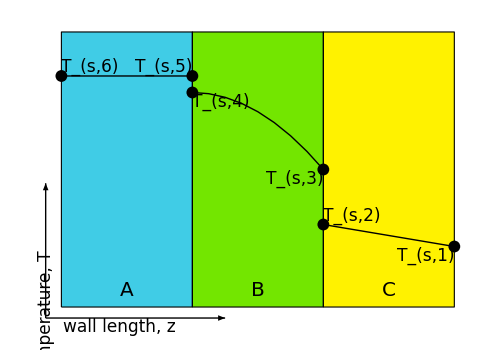

```mathematica
Module[{T1,T2,LA,LB,LC,Ts6,Ts5,Ts4,Ts3,Ts2,Ts1,colA,colB,colC},
T1=25;T2=275;
LA=25;LB=25;LC=25;

Ts6=235;Ts5=235;Ts4=220;Ts3=150;Ts2=100;Ts1=80;

colA=RGBColor[0.25,0.8,0.9];colB=RGBColor[0.45,0.9,0];
colC=RGBColor[1,0.95,0];

Graphics[{
{EdgeForm@Black,
colA,Rectangle[{0,T1},{LA,T2}],
colB,Rectangle[{LA,T1},{LA+LB,T2}],
colC,Rectangle[{LA+LB,T1},{LA+LB+LC,T2}]},

{Thick,Line[{{0,Ts6},{LA,Ts5}}],BezierCurve[{{LA,Ts4},{LA+0.5*LB,Ts4},{LA+LB,Ts3}}],Line[{{LA+LB,Ts2},{LA+LB+LC,Ts1}}]},

{PointSize@0.017,Point@{{0,Ts6},{LA,Ts5},{LA,Ts4},{LA+LB,Ts3},{LA+LB,Ts2},{LA+LB+LC,Ts1}}},

Text[Style[Subscript[Style["T",Italic],Row@{"s,",#1}],17],#2,1.2*#3]&@@@{{6,{0,Ts6},{-1,-1}},{5,{LA,Ts5},{1,-1}},{4,{LA,Ts4},{-1,1}},{3,{LA+LB,Ts3},{1,1}},{2,{LA+LB,Ts2},{-1,-1}},{1,{LA+LB+LC,Ts1},{1,1}}},

Text[Style[#1,20],{#2,T1+15}]&@@@{{"A",0.5*LA},{"B",LA+0.5*LB},{"C",LA+LB+0.5*LC}},

Arrow[{{-3,T1-10},{-3,0.5*T2}}],Arrow[{{-3,T1-10},{LA+0.25*LB,T1-10}}],
Text[Style[Row@{"wall length, ",Style["z",Italic]},17],{-3+0.5*(LA+0.25*LB-3),T1-10},{0,1.5}],
Text[Rotate[Style[Row@{"temperature, ",Style["T",Italic]},17],90°],{-3,T1-10+0.5*(0.5*T2-(T1-10))},{1.5,0}]

},ImageSize->{500,350},AspectRatio->Full,PlotRangePadding->Scaled@0.05]
]
```